1266

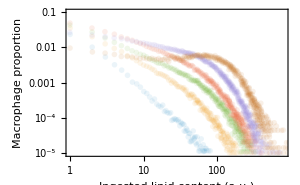

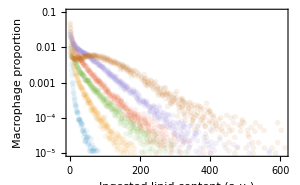

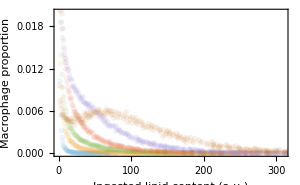

```mathematica
(* resampled experimental data *)
SetDirectory[NotebookDirectory[]];

resamplet0=Join[{{0,1(1-0.05436408687995582)}},Drop[Import["full_initconds.csv","CSV"],1]];
resamplet12=Join[Drop[Import["t12_full.csv"],1]];
resamplet24=Join[Drop[Import["t24_full.csv"],1]];
resamplet36=Join[Drop[Import["t36_full.csv"],1]];
resamplet48=Join[Drop[Import["t48_full.csv"],1]];
resamplet60=Join[Drop[Import["t60_full.csv"],1]];
resamples={resamplet0,resamplet12,resamplet24,resamplet36,resamplet48,resamplet60};

Mdata={{0,1.},{12,0.9762773162434892},{24,0.8759123513425332},{36,0.7481751232867709},{48,0.49635031618480696},{60,0.14233568487147408}};

lipiddata=Drop[Import["avg_LipidContent_data.csv"],1];
lipiddata=Table[{Round[d[[1]]],d[[2]]},{d,lipiddata}];

distributionplot=ListPlot[resamples,PlotRange->{{1,300},{10^(-5),0.01}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (hours)", "Proportion of macrophages"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black}];
Mplot=ListPlot[Mdata,PlotMarkers->Automatic,PlotTheme->"Scientific",BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Time t (hours)", "Macrophage surviving fraction"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black}];
Lplot=ListPlot[lipiddata,PlotMarkers->Automatic,PlotTheme->"Scientific",FrameLabel->{"Time t (hours)", "Mean ingested lipid content (a.u.)"},BaseStyle->{FontFamily->"Cambria Math"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black}];

ndatapoints=Length@resamplet12+Length@resamplet24+Length@resamplet36+Length@resamplet48+Length@resamplet60+(Length@Mdata-1)
{Mplot,Lplot,distributionplot};

opacityval=0.1;
distributionloglogplot=ListLogLogPlot[resamples,PlotRange->{{1,800},{10^(-5),0.1}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300(*,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"}*),PlotStyle->{Opacity[opacityval]}]

distributionloglinearplot=ListPlot[resamples,PlotRange->{{1,610},{10^(-5),0.1}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300(*,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"}*),ScalingFunctions->{"Linear","Log"},PlotStyle->{Opacity[opacityval]}]

distributionlinearplot=ListPlot[resamples,PlotRange->{{0,310},{0,0.02}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300(*,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"}*),ScalingFunctions->{"Linear","Linear"},PlotStyle->{Opacity[opacityval]}]

distributionloglogplot48=ListLogLogPlot[Most@resamples,PlotRange->{{1,500},{10^(-5),0.1}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300(*,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"}*),PlotStyle->{Opacity[opacityval]}];

distributionloglinearplot48=ListPlot[Most@resamples,PlotRange->{{1,610},{10^(-5),0.1}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300(*,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"}*),ScalingFunctions->{"Linear","Log"},PlotStyle->{Opacity[opacityval]}];

distributionlinearplot48=ListPlot[Most@resamples,PlotRange->{{0,310},{0,0.02(*0.02*)}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300,(*PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"},*)ScalingFunctions->{"Linear","Linear"},PlotStyle->{Opacity[opacityval]}];

negbinom[i_,μ_,cv_]:=Module[{r,p},
r=(μ-1)^2/(cv^2*μ^2-μ+1);
p=(μ-1)/(cv^2*μ^2);
Binomial[i+r-2,i-1]*p^r*(1-p)^(i-1)]

decay[i_?IntegerQ,a_,b_]:=Module[{r,p},
k=(*Sum[N@(j)^(-b),{j,1,1000}];*)Zeta[b];
(1/k)*(i)^(-b)
]

logit[x_]:=Log[x/(1-x)];
invlogit[x_]:=1/(1+Exp[-x]);
```

```mathematica
(* Log-likelihood function *)
ClearAll[fullloglikelihood];

fullloglikelihood[{e_?NumericQ,μ_?NumericQ,cv_?NumericQ,β0_?NumericQ,β1_?NumericQ,q_?NumericQ,σM_?NumericQ,σm_?NumericQ}]:=
Module[{imax,dx,tmax,n,idx,pmf,βvec,ηvec,fvec,fbar,mInit,eqs,sol,Msol,moutput,Moutput,Loutput,loglikelihoodM,loglikelihoodm,outcome,λ},

rhsVecfunction[v_?VectorQ,βvec_?VectorQ,ηvec_?VectorQ,fvec_?VectorQ,ee_,fbar_,idx_?VectorQ,n_?IntegerQ]:=Module[{betaBar,etaBar,alpha,conv}, (* Here v = (m[0], m[1], ..., m[imax] *)
betaBar=Dot[βvec,v];(* <beta>*)
etaBar=Dot[ηvec,v];(* <Subscript[η, l]>*)
alpha=Dot[βvec*(ee+idx),v]/(fbar*etaBar);(* <beta_i (e+i)> /fbar*)
conv=Prepend[Take[ListConvolve[fvec,ηvec*v,{1,-1},0],n-1],0];(*conv[[i+1]]=Sum_{j=1}^i f_j η_{i-j} m_{i-j} for i>=1*)
alpha (conv-ηvec*v)+(betaBar-βvec)*v
];

imax=1000;
tmax=50;
n=imax+1;
idx=Range[0,imax];


(*βvec=Developer`ToPackedArray@N@(Table[β0,{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@(Table[β0*Exp [β1*t],{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@(Table[β0*Exp [(β1*t)^2],{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@(Table[β0*Exp [(β1*t)^(1/2)],{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@(Table[β1/(1+(β1-β0)/β0*Exp[-t/q]),{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@(β0+β1*idx);*)
(*βvec=Developer`ToPackedArray@N@(β0+β1*idx^q);*)
(*βvec=Developer`ToPackedArray@N@(β0+β1*idx^(1/2));*)
(*βvec=Developer`ToPackedArray@N@(β1/(1+(β1-β0)/β0*Exp[-idx/q]));*)
(*βvec=Developer`ToPackedArray@N@(β0*Exp [q*t]+β1*idx);*)
βvec=Developer`ToPackedArray@N@((β0+(β1-β0)*(1-Exp[-idx/q])));
(*βvec=Developer`ToPackedArray@N@((β0+(β1-β0)*(1-Exp[-idx^2/q^2])));*)


ηvec=Developer`ToPackedArray@N@(Table[1,{i,1,Length[idx]}]);
(*ηvec=Developer`ToPackedArray@N@(Table[Exp[-q*t],{i,1,Length[idx]}]);*)
(*ηvec=Developer`ToPackedArray@N@((Exp[-r*idx]));*)
(*ηvec=Developer`ToPackedArray@N@((Exp[-r*idx^2]));*)

fvec=Developer`ToPackedArray@N@(negbinom[#,μ,cv](*decay[#,μ,cv]*)(*pmf[#,λ]*)&/@(idx+1));

mInit=Developer`ToPackedArray@N@PadRight[resamplet0[[All,2]],n,0];
eqs={u'[t]==rhsVecfunction[u[t],βvec,ηvec,fvec,e,μ,idx,n],u[0]==mInit,M'[t]==-M[t] (βvec.u[t]),M[0]==1};

outcome=0;
sol=NDSolve[{eqs,WhenEvent[Total[u[t]]<0.99,"StopIntegration";outcome=1]},{u,M},{t,0,tmax}];

moutput=Table[u[t]/. sol[[1]],{t,{0,12,24,36,48}}];
Moutput=Table[M[t]/. sol[[1]],{t,{0,12,24,36,48}}];
Loutput=Table[idx.(u[t]/. sol[[1]]),{t,{0,12,24,36,48}}];

loglikelihoodM=Sum[-Log[Mdata[[i]][[2]]*(1-Mdata[[i]][[2]])*σM*Sqrt[2 Pi]]-1/(2*σM^2)*(Log[Mdata[[i]][[2]]/(1-Mdata[[i]][[2]])]-Log[Moutput[[i]]/(1-Moutput[[i]])])^2,{i,2,5}];

loglikelihoodm=Sum[1/Length[resamples[[j]]]*Sum[-Log[resamples[[j]][[i]][[2]]*(1-resamples[[j]][[i]][[2]])*(σm*Sqrt[12*(j-1)])*Sqrt[2 Pi]]-1/(2*(σm*Sqrt[12*(j-1)])^2)*(Log[resamples[[j]][[i]][[2]]/(1-resamples[[j]][[i]][[2]])]-Log[moutput[[j]][[Round[resamples[[j]][[i]][[1]]]+1]]/(1-moutput[[j]][[Round[resamples[[j]][[i]][[1]]]+1]])])^2,{i,1,Length[resamples[[j]]]}],{j,2,5}];

If[outcome==0&&Element[loglikelihoodM+loglikelihoodm,Reals],loglikelihoodM+loglikelihoodm,-10^(6)]
]


fullplots[{e_?NumericQ,μ_?NumericQ, cv_?NumericQ,β0_?NumericQ,β1_?NumericQ,q_?NumericQ,σM_?NumericQ,σm_?NumericQ}]:=
Module[{imax,dx,tmax,n,idx,pmf,βvec,ηvec,fvec,fbar,mInit,eqs,sol,Msol,moutput,Moutput,loglikelihoodm,loglikelihoodM,outcome,λ,modeldistributionplot,modelMplot,modelLplot,grid,Loutput,modeldistributionplotloglinear,modeldistributionplotloglog},


rhsVecfunction[v_?VectorQ,βvec_?VectorQ,ηvec_?VectorQ,fvec_?VectorQ,ee_,fbar_,idx_?VectorQ,n_?IntegerQ]:=Module[{betaBar,etaBar,alpha,conv}, (* Here v = (m[0], m[1], ..., m[imax] *)
betaBar=Dot[βvec,v];(* <beta>*)
etaBar=Dot[ηvec,v];(* <Subscript[η, l]>*)
alpha=Dot[βvec*(ee+idx),v]/(fbar*etaBar);(* <beta_i (e+i)> /fbar*)
conv=Prepend[Take[ListConvolve[fvec,ηvec*v,{1,-1},0],n-1],0];(*conv[[i+1]]=Sum_{j=1}^i f_j η_{i-j} m_{i-j} for i>=1*)
alpha (conv-ηvec*v)+(betaBar-βvec)*v
];

imax=1000;
tmax=50;
n=imax+1;
idx=Range[0,imax];

(*βvec=Developer`ToPackedArray@N@(Table[β0,{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@(Table[β0*Exp [β1*t],{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@(Table[β0*Exp [(β1*t)^2],{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@(Table[β0*Exp [(β1*t)^(1/2)],{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@(Table[β1/(1+(β1-β0)/β0*Exp[-t/q]),{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@(β0+β1*idx);*)
(*βvec=Developer`ToPackedArray@N@(β0+β1*idx^q);*)
(*βvec=Developer`ToPackedArray@N@(β0+β1*idx^(1/2));*)
(*βvec=Developer`ToPackedArray@N@(β1/(1+(β1-β0)/β0*Exp[-idx/q]));*)
(*βvec=Developer`ToPackedArray@N@(β0*Exp [q*t]+β1*idx);*)
βvec=Developer`ToPackedArray@N@((β0+(β1-β0)*(1-Exp[-idx/q])));
(*βvec=Developer`ToPackedArray@N@((β0+(β1-β0)*(1-Exp[-idx^2/q^2])));*)


ηvec=Developer`ToPackedArray@N@(Table[1,{i,1,Length[idx]}]);
(*ηvec=Developer`ToPackedArray@N@(Table[Exp[-q*t],{i,1,Length[idx]}]);*)
(*ηvec=Developer`ToPackedArray@N@((Exp[-r*idx]));*)
(*ηvec=Developer`ToPackedArray@N@((Exp[-r*idx^2]));*)

fvec=Developer`ToPackedArray@N@(negbinom[#,μ,cv](*decay[#,μ,cv]*)(*pmf[#,λ]*)&/@(idx+1));

mInit=Developer`ToPackedArray@N@PadRight[resamplet0[[All,2]],n,0];

eqs={u'[t]==rhsVecfunction[u[t],βvec,ηvec,fvec,e,μ,idx,n],u[0]==mInit,M'[t]==-M[t] (βvec.u[t]),M[0]==1};

outcome=0;
sol=NDSolve[{eqs,WhenEvent[Total[u[t]]<0.99,"StopIntegration";outcome=1]},{u,M},{t,0,tmax}];

moutput=Table[u[t]/. sol[[1]],{t,{0,12,24,36,48}}];
moutput=Table[Table[{idx[[i]],d[[i]]},{i,1,Length[d]}],{d,moutput}];

modeldistributionplot=ListPlot[moutput,PlotRange->{{0,310},{10^(-5),All}},ImageSize->300,Joined->True,ScalingFunctions->{"Linear","Linear"}];
modeldistributionplotloglinear=ListPlot[moutput,PlotRange->{{0,1000},{10^(-5),All}},ImageSize->300,Joined->True,ScalingFunctions->{"Linear","Log"}];
modeldistributionplotloglog=ListPlot[moutput,PlotRange->{{0,800},{10^(-5),All}},ImageSize->300,Joined->True,ScalingFunctions->{"Log","Log"}];


modeldistributionplot=ListPlot[moutput,PlotRange->{{0,300},{0,All}},ImageSize->300,Joined->True];
modelMplot=Plot[{M[t]/. sol[[1]],invlogit[logit[M[t]/. sol[[1]]]+Quantile[NormalDistribution[0,σM],0.025]],invlogit[logit[M[t]/. sol[[1]]]+Quantile[NormalDistribution[0,σM],0.975]]},{t,0,60},PlotRange->{{-0.5,50},{-0.05,1.05}},PlotStyle->{Automatic,{Dashed,Thin,Opacity[0]},{Dashed,Thin,Opacity[0]}},Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.1],ImageSize->300,BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Time \!\(\*StyleBox[\"t\",FontSlant->\"Italic\"]\)\!\(\*StyleBox[\" \",FontSlant->\"Italic\"]\)(hours)","Cell population M̂"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Frame->True];
modelLplot=Plot[{idx.(u[t]/. sol[[1]]),(idx.(u[t]/. sol[[1]]))*Quantile[LogNormalDistribution[0,σL],0.025],(idx.(u[t]/. sol[[1]]))*Quantile[LogNormalDistribution[0,σL],0.975]},{t,0,50},PlotRange->{{-0.5,50},{-0.05,50}},PlotStyle->{Automatic,{White,Dashed,Thin,Opacity[0]},{White,Dashed,Thin,Opacity[0]}},Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.1],ImageSize->300,BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Time t (hours)", "Mean ingested lipid (L̂)_M (a.u.)"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Frame->True];


Grid[{{Show[modelMplot,Mplot],Show[modelLplot,Lplot]},{Show[distributionlinearplot48,modeldistributionplot],Show[distributionloglinearplot48,modeldistributionplotloglinear](*,Show[distributionloglogplot48,modeldistributionplotloglog]*)}}]
]
```

```mathematica
OverHat[M]
```

M̂

```mathematica
(* β = β0 *)
nstep=1;
{eval,μval,cvval,β0val,σMval,σmval}={0.2,0.2,2,1/80,0.2,0.2};
NMaximize[{fullloglikelihood[{100*e,100*μ,cv,β0,0,1,σM,σm}],0.01<e<1,0.01<μ<1, 0.5<cv<3,0.001<β0<1,0.01<σM<1,0.01<σm<1},{e,μ, cv,β0,σM,σm},Method->{Automatic,"InitialPoints"->{{eval,μval,cvval,β0val,σMval,σmval}}},StepMonitor:>If[Mod[++nstep,50]==0,Print["Current x: ",{{e,μ,cv,β0,σM,σm},fullloglikelihood[{100*e,100*μ,cv,β0,0,1,σM,σm}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.319634,0.392274,2.31696,0.00706736,0.764861,0.227231},31.6847}

Current x: {{0.326597,0.255737,1.97912,0.00705499,0.739752,0.156707},32.6426}

Current x: {{0.331946,0.220607,1.9513,0.00673873,0.812126,0.142599},32.7826}

{32.8636,{e→0.354513,μ→0.112853,cv→2.84681,β0→0.00670571,σM→0.804075,σm→0.140065}}

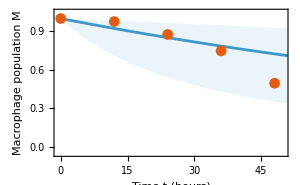
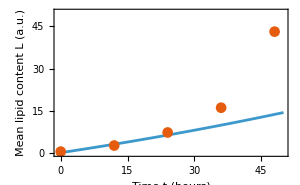
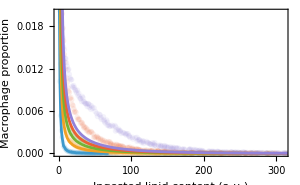
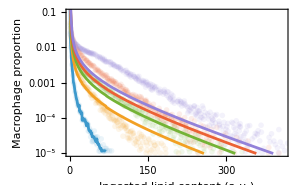
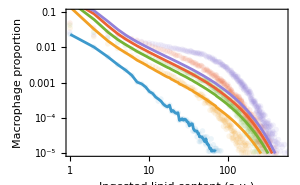
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
{eval,μval,cvval,β0val,σMval,σmval}={e,μ,cv,β0,σM,σm}/.{e->0.3545134487198656,μ->0.11285286899467654,cv->2.846813303848286,β0->0.006705708433480718,σM->0.8040752645099549,σm->0.1400653224286472};

fullplots[{100*eval,100*μval,cvval,β0val,0,1,σMval,σmval}]
```

```mathematica
(* β = β0*Exp [β1*t] *)
nstep=1;
{eval,μval,cvval,β0val,β1val,σMval,σmval}={0.2,0.2,2,0.3,0.05,0.5,0.5};
NMaximize[{fullloglikelihood[{100*e,100*μ,cv,β0/100,β1,1,σM,σm}],0.01<e<1,0.01<μ<1, 0.5<cv<3,0.001<β0<1,0.001<β1<1,0.01<σM<1,0.01<σm<1},{e,μ, cv,β0,β1,σM,σm},Method->{Automatic,"InitialPoints"->{{eval,μval,cvval,β0val,β1val,σMval,σmval}}},StepMonitor:>If[Mod[++nstep,50]==0,Print["Current x: ",{{e,μ,cv,β0,β1,σM,σm},fullloglikelihood[{100*e,100*μ,cv,β0/100,β1,1,σM,σm}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.732367,0.230106,1.57735,0.172962,0.0611783,0.487614,0.107183},37.3192}

Current x: {{0.672019,0.132333,2.0482,0.15246,0.0719213,0.428641,0.0857627},38.7184}

Current x: {{0.516323,0.0804768,2.82771,0.164266,0.072478,0.228504,0.0847848},40.4135}

Current x: {{0.501072,0.0787915,2.89953,0.162361,0.0727455,0.204709,0.0868634},40.4718}

Current x: {{0.54322,0.0724031,2.93056,0.159453,0.0734279,0.180674,0.0875947},40.5962}

Current x: {{0.557354,0.0742014,2.90211,0.159702,0.0730527,0.183332,0.0914443},40.6203}

$Aborted

```mathematica
{eval,μval,cvval,β0val,β1val,σMval,σmval}={0.5573536796257026,0.07420136575187686,2.9021051520279606,0.1597020419966544,0.07305271713214405,0.18333234388940944,0.09144432825781657};
FindMaximum[{fullloglikelihood[{100*e,100*μ,cv,β0/100,β1,1,σM,σm}],0.01<e<1,0.01<μ<1,0.5<cv<3,0.001<β0<1,0.001<β1<1,0.01<σM<1,0.01<σm<1},{{e,eval},{μ,μval},{cv,cvval},{β0,β0val},{β1,β1val},{σM,σMval},{σm,σmval}},StepMonitor:>If[Mod[++nstep,1]==0,Print["Current x: ",{{e,μ,cv,β0,β1,σM,σm},fullloglikelihood[{100*e,100*μ,cv,β0/100,β1,1,σM,σm}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.528595,0.145541,1.99912,0.158724,0.0734558,0.177067,0.0861934},40.8585}

Current x: {{0.528596,0.145538,1.99915,0.158724,0.0734558,0.177068,0.0861935},40.8585}

Current x: {{0.528606,0.145509,1.99937,0.158724,0.0734557,0.177065,0.0861918},40.8585}

Current x: {{0.528606,0.145509,1.99937,0.158724,0.0734557,0.177065,0.0861918},40.8585}

{40.8585,{e→0.528606,μ→0.145509,cv→1.99937,β0→0.158724,β1→0.0734557,σM→0.177065,σm→0.0861918}}

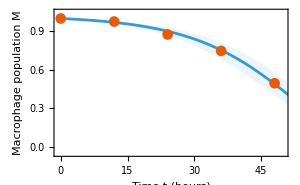
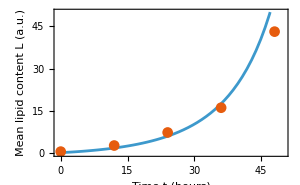
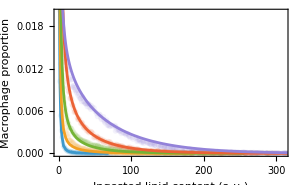
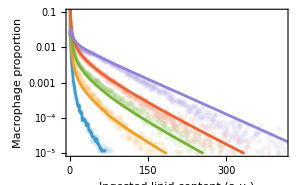
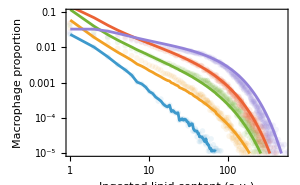
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
fullplots[{100*e,100*μ,cv,β0/100,β1,1,σM,σm}/.{e->0.5286062183817707,μ->0.1455088428748961,cv->1.9993747328174223,β0->0.15872415807247975,β1->0.07345566803880664,σM->0.17706496337029562,σm->0.08619177018275748}]
```

```mathematica
(* β = β0 + β1*idx *)
nstep=1;
{eval,μval,cvval,β0val,β1val,σMval,σmval}={0.431,0.363,0.89,0.33,0.1,0.5,0.5};
FindMaximum[{fullloglikelihood[{100*e,100*μ,cv,β0/100,β1/100,1,σM,σm}],0.01<e<1,0.01<μ<1,0.1<cv<3,0.001<β0<1,0.001<β1<1,0.01<σM<1,0.01<σm<1},{{e,eval},{μ,μval},{cv,cvval},{β0,β0val},{β1,β1val},{σM,σMval},{σm,σmval}},StepMonitor:>If[Mod[++nstep,1]==0,Print["Current x: ",{{e,μ,cv,β0,β1,σM,σm},fullloglikelihood[{100*e,100*μ,cv,β0/100,β1/100,1,σM,σm}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.528713,0.216009,1.96861,0.154718,0.116257,0.211346,0.0860429},40.1574} (* cycle of convergence *)

```mathematica
nstep=1;
{eval,μval,cvval,β0val,β1val,σMval,σmval}={0.45,0.2160087910332719,1.9686094388949378,0.15471757762320495,0.11625650359165779,0.21134634888711168,0.08604293379046177};
NMaximize[{fullloglikelihood[{100*e,100*μ,cv,β0/100,β1/100,1,σM,σm}],0.01<e<1,0.01<μ<1,0.1<cv<3,0.01<β0<1,0.01<β1<0.3,0.01<σM<1,0.01<σm<1},{e,μ,cv,β0,β1,σM,σm},Method->{Automatic,"InitialPoints"->{{eval,μval,cvval,β0val,β1val,σMval,σmval}}},StepMonitor:>If[Mod[++nstep,50]==0,Print["Current x: ",{{e,μ,cv,β0,β1,σM,σm},fullloglikelihood[{100*e,100*μ,cv,β0/100,β1/100,1,σM,σm}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.466906,0.230746,1.96716,0.197066,0.116677,0.273372,0.0875304},39.5841}

Current x: {{0.486234,0.20892,2.05005,0.1674,0.122856,0.229012,0.0810773},40.0161}

Current x: {{0.506915,0.211027,2.0273,0.154395,0.121594,0.209075,0.0881705},40.1313}

$Aborted

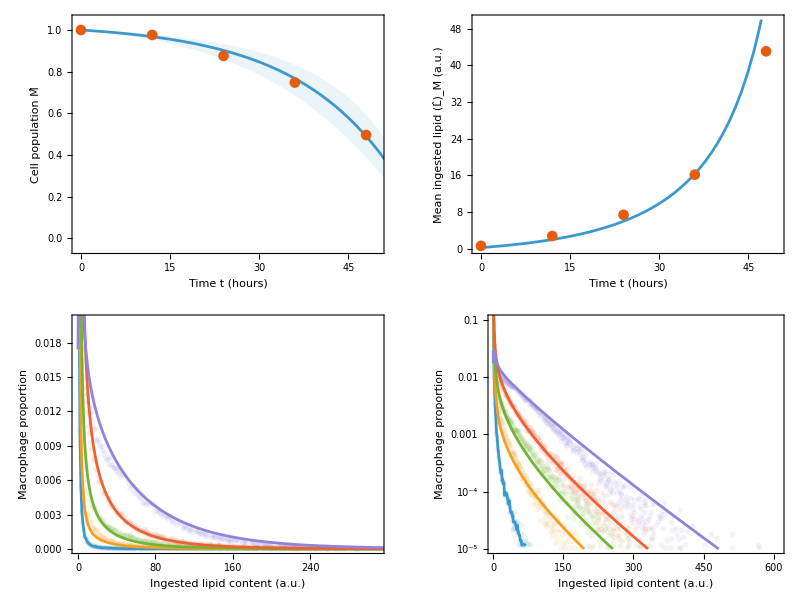

```mathematica
{eval,μval,cvval,β0val,β1val,σMval,σmval}={0.5287129603284024,0.2160087910332719,1.9686094388949378,0.15471757762320495,0.11625650359165779,0.21134634888711168,0.08604293379046177};
fullplots[{100*eval,100*μval,cvval,β0val/100,β1val/100,1,σMval,σmval}]
```

```mathematica
(* β=β1/(1+(β1-β0)/β0*Exp[-t/q]):Saturating time-dependent death rate *)
nstep=1;
{eval,μval,cvval,β0val,β1val,qval,σMval,σmval}={0.4219478064913914,0.12409364460180135,2.2598424652364835,0.22744704958552608,5.715708854892685,13.345479531814572,0.028441763612793405,0.07717047413528919};
FindMaximum[{fullloglikelihood[{100*e,100*μ,cv,β0/100,β1/100,q,σM,σm}],0.1<e<1,0.01<μ<1,0.1<cv<3,0.01<β0<1,0.01<β1<10,0.1<q<100,0.01<σM<1,0.01<σm<1},{{e,eval},{μ,μval},{cv,cvval},{β0,β0val},{β1,β1val},{q,qval},{σM,σMval},{σm,σmval}},StepMonitor:>If[Mod[++nstep,1]==0,Print["Current x: ",{{e,μ,cv,β0,β1,q,σM,σm},fullloglikelihood[{100*e,100*μ,cv,β0/100,β1/100,q,σM,σm}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.547417,0.154071,1.90125,0.10152,3.3734,8.33188,0.119755,0.0893378},42.2796}

Current x: {{0.547441,0.154002,1.90173,0.101515,3.37317,8.33155,0.11975,0.0893349},42.2796}

{42.2796,{e→0.547441,μ→0.154002,cv→1.90173,β0→0.101515,β1→3.37317,q→8.33155,σM→0.11975,σm→0.0893349}}

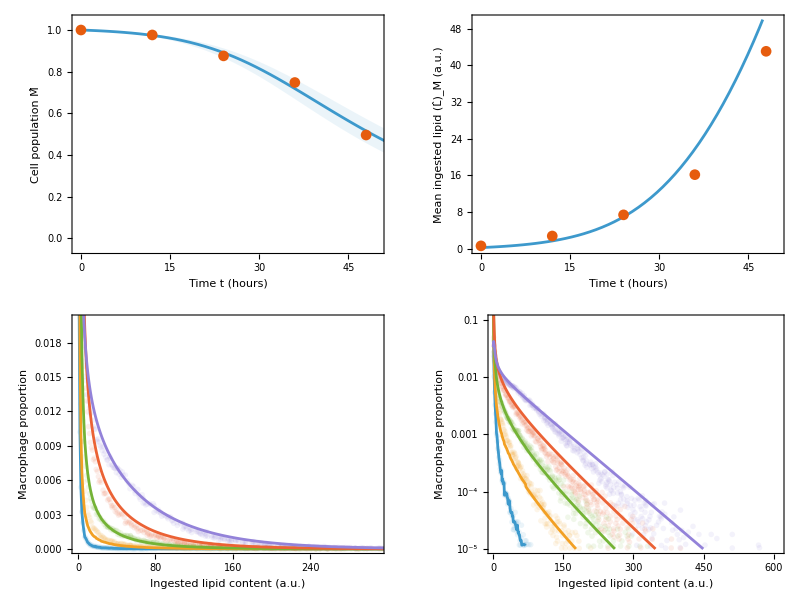

```mathematica
fullplots[{100*e,100*μ,cv,β0/100,β1/100,q,σM,σm}/.{e->0.5474411415249859,μ->0.1540017845063153,cv->1.901727155522228,β0->0.10151531079350407,β1->3.37316547096781,q->8.331547512030825,σM->0.11975004073712367,σm->0.08933492225016373}]
```

```mathematica
(* β=β1/(1+(β1-β0)/β0*Exp[-idx/q]: Saturating lipid-dependent death rate *)
nstep=1;
{eval,μval,cvval,β0val,β1val,qval,σMval,σmval}={0.49508553527935056,0.2677993290928105,1.4041322208746279,0.1392659839671243,0.10000015969231896,5.084241586157121,0.18901613123513317,0.09229789124190083};
FindMaximum[{fullloglikelihood[{100*e,100*μ,cv,β0/100,β1,q,σM,σm}],0.1<e<1,0.01<μ<1,0.1<cv<3,0.01<β0<1,0.1<β1<100,0.1<q<100,0.01<σM<1,0.01<σm<1},{{e,eval},{μ,μval},{cv,cvval},{β0,β0val},{β1,β1val},{q,qval},{σM,σMval},{σm,σmval}},StepMonitor:>If[Mod[++nstep,1]==0,Print["Current x: ",{{e,μ,cv,β0,β1,q,σM,σm},fullloglikelihood[{100*e,100*μ,cv,β0/100,β1,q,σM,σm}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.45,0.22,1.62,0.227447,0.11,8.1,0.3,0.3},35.7208}

Current x: {{0.472977,0.233583,1.61782,0.156831,0.148807,8.09807,0.241248,0.12861},38.9685}

Current x: {{0.486609,0.242835,1.60859,0.159949,0.147229,8.09983,0.211788,0.0830882},39.793}

Current x: {{0.50404,0.246404,1.56997,0.165316,0.134534,8.09896,0.214001,0.0876373},39.9775}

Current x: {{0.498866,0.288669,1.38818,0.163495,0.13787,8.26586,0.211569,0.0882116},40.0112}

Current x: {{0.508126,0.294136,1.37311,0.16304,0.134272,8.25795,0.21142,0.0904109},40.0322}

Current x: {{0.506684,0.273277,1.41065,0.156165,0.117307,7.01434,0.204478,0.0911082},40.1418}

Current x: {{0.49687,0.293701,1.33763,0.150568,0.116646,6.59344,0.199275,0.0927843},40.1638}

Current x: {{0.498478,0.289411,1.35533,0.150886,0.115647,6.56153,0.19999,0.0926483},40.1722}

Current x: {{0.497397,0.270582,1.38937,0.1416,0.100044,5.23985,0.190827,0.0926731},40.318}

Current x: {{0.494577,0.267071,1.40738,0.139329,0.100257,5.09124,0.189014,0.0922847},40.3205}

Current x: {{0.495212,0.268132,1.40331,0.139519,0.100263,5.11229,0.189246,0.0923092},40.3206}

Current x: {{0.495224,0.268179,1.40313,0.139522,0.100263,5.11273,0.189248,0.0923105},40.3206}

Current x: {{0.495285,0.268346,1.40241,0.139532,0.100264,5.11463,0.189245,0.0923107},40.3205}

Current x: {{0.495255,0.268262,1.40277,0.139527,0.100264,5.11366,0.189247,0.0923106},40.3206}

Current x: {{0.495093,0.267816,1.40408,0.139277,0.100011,5.08547,0.189025,0.0922986},40.3233}

Current x: {{0.495093,0.267819,1.40408,0.139279,0.100014,5.08573,0.189028,0.0922986},40.3233}

Current x: {{0.495085,0.267799,1.40413,0.139266,0.1,5.08424,0.189016,0.0922979},40.3234}

Current x: {{0.495086,0.267799,1.40413,0.139266,0.1,5.08424,0.189016,0.0922979},40.3234}

{40.3234,{e→0.495086,μ→0.267799,cv→1.40413,β0→0.139266,β1→0.1,q→5.08424,σM→0.189016,σm→0.0922979}}

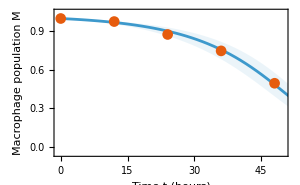
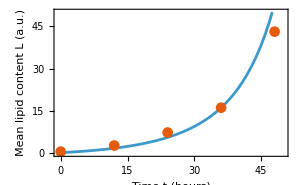
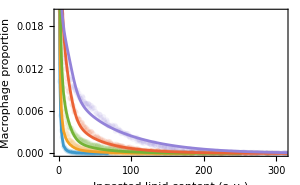
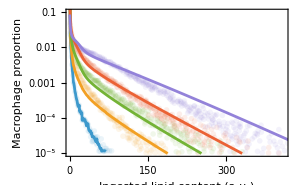
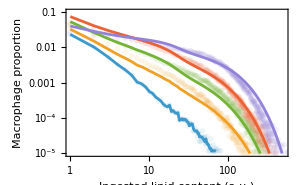
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
fullplots[{100*e,100*μ,cv,β0/100,β1,q,σM,σm}/.{e->0.49508553527935056,μ->0.2677993290928105,cv->1.4041322208746279,β0->0.1392659839671243,β1->0.10000015969231896,q->5.084241586157121,σM->0.18901613123513317,σm->0.09229789124190083}]
```

```mathematica
(* β=β0 + (β1-β0)*Exp[-idx/q]: Saturating lipid-dependent death rate *)
nstep=1;
{eval,μval,cvval,β0val,β1val,qval,σMval,σmval}={0.5789979830209905,0.09930430409569022,2.367914552261123,0.01000051165458577,0.03202540582994149,2.3003450111156925,0.1260111240259285,0.0909299024305862};
FindMaximum[{fullloglikelihood[{100*e,100*μ,cv,β0/100,β1,q,σM,σm}],0.1<e<1,0.01<μ<1,0.1<cv<3,0.001<β0<0.1,0.001<β1<1,0.1<q<100,0.01<σM<1,0.01<σm<1},{{e,eval},{μ,μval},{cv,cvval},{β0,β0val},{β1,β1val},{q,qval},{σM,σMval},{σm,σmval}},StepMonitor:>If[Mod[++nstep,1]==0,Print["Current x: ",{{e,μ,cv,β0,β1,q,σM,σm},fullloglikelihood[{100*e,100*μ,cv,β0/100,β1,q,σM,σm}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.573852,0.103656,2.3199,0.0010007,0.0315044,1.88175,0.125561,0.0906306},42.0325}

Current x: {{0.573852,0.103656,2.3199,0.0010007,0.0315043,1.88175,0.125561,0.0906306},42.0325}

{42.0325,{e→0.573852,μ→0.103656,cv→2.3199,β0→0.0010007,β1→0.0315043,q→1.88175,σM→0.125561,σm→0.0906306}}

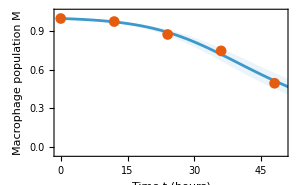
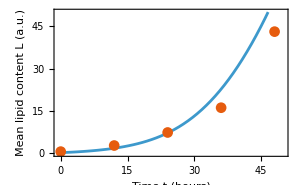
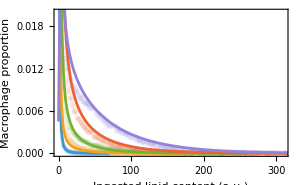
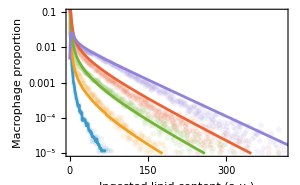
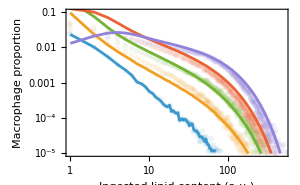
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
fullplots[{100*e,100*μ,cv,β0/100,β1,q,σM,σm}/.{e->0.5789979830209905,μ->0.09930430409569022,cv->2.367914552261123,β0->0.01000051165458577,β1->0.03202540582994149,q->2.3003450111156925,σM->0.1260111240259285,σm->0.0909299024305862}]
```